## Arbitrary input function

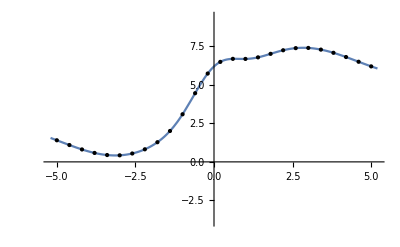

```mathematica
func=2 ⅇ^(-x^2)+2 Sin[0.1+0.67 x]-.25(-16-9x/4);
tab={#,func/.x->#}&/@Subdivide[-5,5,75]; (* discretized data *)
 
Plot[func,{x,-5.2,5.2},PlotRange->{-3.9,9.45},Epilog->{Point[tab⟦;;;;3⟧]}]
```

## Training

### Approximation

```mathematica
n=6; (* number of neurons *)
f[x_]:=1/(1+Exp[-x]); (* activation function (sigmoid) *)
basisF=A f[a x+b]; (* neuron with linear connections: a/b = weight/bias on the first linear layer = horizontal scale/offset; A = weight on the second linear layer = vertical scale; (vertical offset is redundant in the this case) *)
```

### Explicit expression for the full model

```mathematica
Clear[x];
vars=ExtractCoefficients[basisF,x];
ExtractCoefficients[expression_,var_]:=Select[Union[Level[expression,{-1}]],!(#===var)&&(N[#]===#)&];
model=Sum[basisF/.(#->ToExpression[ToString[#]~~ToString[i]]&/@vars),{i,n}]
modelvars=ExtractCoefficients[model,x]
```

A1/(1+ⅇ^(-b1-a1 x))+A2/(1+ⅇ^(-b2-a2 x))+A3/(1+ⅇ^(-b3-a3 x))+A4/(1+ⅇ^(-b4-a4 x))+A5/(1+ⅇ^(-b5-a5 x))+A6/(1+ⅇ^(-b6-a6 x))

{a1,A1,a2,A2,a3,A3,a4,A4,a5,A5,a6,A6,b1,b2,b3,b4,b5,b6}

### Fit

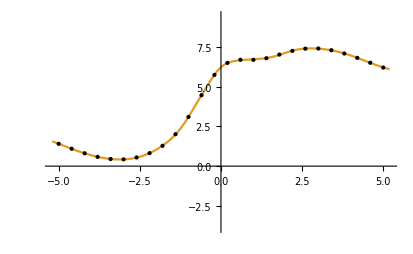

```mathematica
Clear[fit];
fit[x_]=Normal@NonlinearModelFit[tab,model,modelvars,x]//Quiet;

Plot[{,fit[x]},{x,-5.2,5.2},PlotRange->{-3.9,9.45},Epilog->{Point[tab⟦;;;;3⟧]}]
```

### Individual neuron contributions

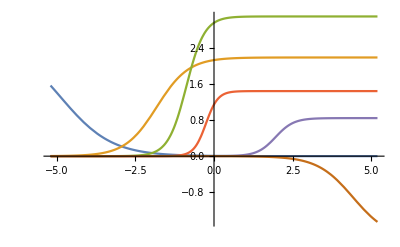

```mathematica
components=SortBy[List@@fit[x],-Part[#,2,1,2,2,1]/Part[#,2,1,2,2,2,1]&]; (* set animation order *)
Plot[Evaluate[components⟦;;⟧],{x,-5.2,5.2}]
```

## Animation

```mathematica
SmoothStep[t_]:=t^2(3-2t);
Needs["MaTeX`"];
xTeX=MaTeX["x"];yTeX=MaTeX["y"];
cc=Graphics[{args__},rest__]:>Graphics[{GrayLevel[.6],args},rest];
```

### Activation function icon

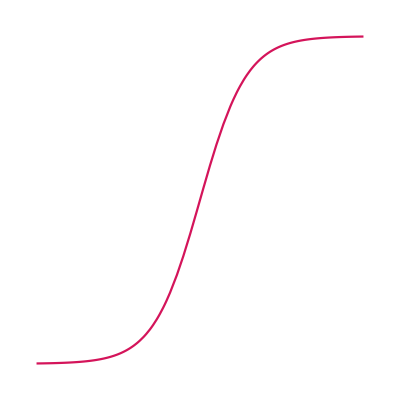

```mathematica
fcol=RGBColor[0.8313725490196079, 0.0784313725490196, 0.35294117647058826];
fpts=Plot[1.5(f[7 x]-.5),{x,-1,1}]⟦1,1,1,3,1,2,1⟧;
ListLinePlot[fpts,PlotStyle->fcol,AspectRatio->1,ImageSize->Tiny,Axes->None]
```

### Fit plot

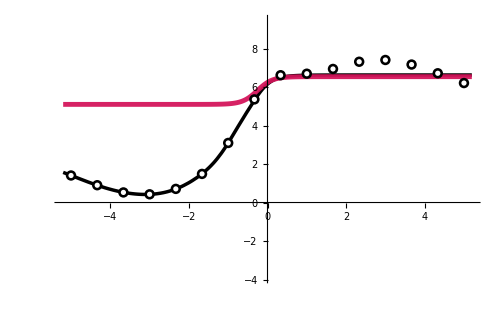

```mathematica
FitPlot[i1_,t_]:=Module[{α1,α2,i},
i=Min[i1,Length[components]]; (* current number of neurons *)
α1=-Sign[components⟦i⟧/.x->5];
α2=Plus@@Prepend[components,0]⟦;;i⟧/.x->100;
α1=α2+2α1 Abs[(components⟦i⟧/.x->-5)-(components⟦i⟧/.x->5)]; (* vertical offset for the current neuron function *)

Show[{
Plot[{
Plus@@Prepend[components,0]⟦;;i⟧+Max[SmoothStep[t],Boole[i1>i]]components⟦i⟧, (* current approximation *)
components⟦i⟧+(α1+(α2-α1) SmoothStep[t]) (* neuron function being added *)
},
{x,-5.2,5.2},PlotRange->{-3.9,9.45},ImagePadding->20,ImageSize->500,
PlotStyle->{
Directive[Black,Thickness[.005]], (* overall approximation style *)
Directive[Opacity[SmoothStep[t]Boole[i1==i],fcol],Thickness[.007]]  (* current neuron function style *)
},
AxesStyle->Directive[Thickness[.004],GrayLevel[.6]],TicksStyle->Thickness[.002],LabelStyle->Directive[Larger],Method->{"AxesInFront"->False}],
Plot[-100,{x,0,1}]
},
PlotRangeClipping->False,Epilog->{
GrayLevel[0],PointSize[.015],Point[tab⟦;;;;5⟧],GrayLevel[1],PointSize[.0075],Point[tab⟦;;;;5⟧], (* discrete points *)
Inset[xTeX,{5.5,1},Automatic,2{1,1}]/.cc,Inset[yTeX,{.5,9.65},Automatic,2{1,1}]/.cc  (* overlay axes labels *)
}] 
];

FitPlot[4,.85]
```

### Fit animation

```mathematica
FitAnimation[t_]:=Module[{t1,T},
T=components//Length;
t1=Clip[(T+1.5)t-.5,{.001,T+1}]; 
FitPlot[Floor[t1]+1,Mod[t1,1]] (* current progression and phase *)
];

Animate[FitAnimation[t],{t,0,1}]
```

### Neural Net diagram

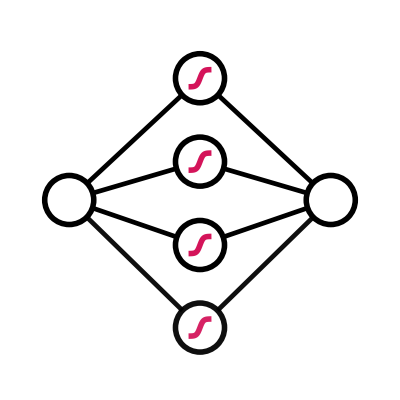

```mathematica
NNdiagram[i1_,t_]:=Module[{i,w=.8,h=1,r=.15,y0=-1.25,ys,yf,Neuron},
i=Min[i1,Length[components]];
yf[n_]:=If[n>0,Mean@{Subdivide[h,-h,n]⟦2;;⟧,Subdivide[h,-h,n]⟦;;-2⟧},{}]; (* vertical distribution function *)
ys=Append[yf[i-1],y0]*(1-SmoothStep[t])+yf[i]*SmoothStep[t]; (* interpolated vertical coordinates for the neurons *)

(* intermediate-layer neuron graphic *)
Neuron[yn_,op_:1]:={
Opacity[op,Black],Thickness[.0085],Line[{{-w,0},{0,yn},{w,0}}], (* connections *) 
Opacity[1,White],EdgeForm[{Thickness[.01],Opacity[op], Black}], Translate[{Disk[{0,0},r], (* main disc *)
Opacity[op,fcol],Thickness[.01],Line[.07 fpts] (* activation function icon *)
},{0,yn}]
}; 
Graphics[{
Neuron/@ys⟦;;-2⟧,Neuron[ys⟦-1⟧,SmoothStep[t]], (* intermediate layer *)
Opacity[1,White],EdgeForm[{Thickness[.01], Black}],
 Disk[{-w,0},r],Inset[xTeX,{-w,0},Automatic,2r{1,1}], (* input node *)
Disk[{w,0},r],Inset[yTeX,{w,0},Automatic,2r{1,1}] (* output node *)
},PlotRange->{{-1,1},{-1,1}}]
];

NNdiagram[4,.85]
```

### Diagram Animation

```mathematica
NNAnimation[t_]:=Module[{t1,T},
T=components//Length;
t1=Clip[(T+1.5)t-.5,{.001,T-.001}]; 
NNdiagram[Floor[t1]+1,Mod[t1,1]] (* current progression and phase *)
];

Animate[NNAnimation[t],{t,0,1}]
```

## Result and Export

### Complete Animation

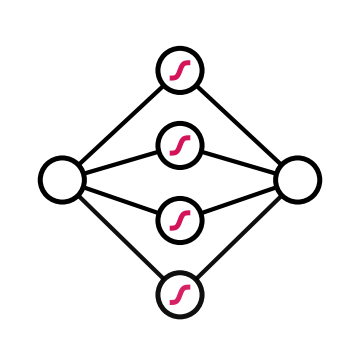
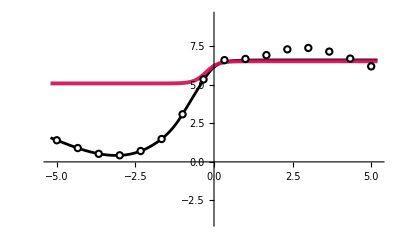

```mathematica
CompoundAnimation[t_]:=Row[{
Show[NNAnimation[t],ImageSize->360],
Show[FitAnimation[t],ImageSize->{Automatic,400}]
}];
CompoundAnimation[.58]
Animate[CompoundAnimation[t],{t,0,1}]
```

### Animation parameters

```mathematica
resolution=900; (* frame width *)
time=8; (* duration *)
fps=25;
```

### Export to PNG sequence

```mathematica
SetDirectory@NotebookDirectory[];
dirname="animation_frames";  (* export directory *)
Quiet@CreateDirectory[dirname]; 

Nframes=Ceiling[fps time]; (* total number of frames *)

Export[
dirname<>"//frame"<>StringPadLeft[ToString[#-1],4,"0"]<>".png", (* filename *)
Rasterize[CompoundAnimation[(#-1.)/Nframes],RasterSize->resolution,Background->White] (* rasterized frame *)
]&/@Range[Nframes];
```